```mathematica
Zeta[2]
```

π^2/6

```mathematica
Sum[j^-s,{j,1,n}]
```

HarmonicNumber[n,s]

```mathematica
D[HarmonicNumber[n,s],n]
```

s (-HarmonicNumber[n,1+s]+Zeta[1+s])

```mathematica
D[Zeta[s]-Zeta[s,n/x+1],x]/.x->1
```

-n s Zeta[1+s,1+n]

```mathematica
D[1/j^s - 1/(j+n)^s - x/(x j)^s+x/(x j+n)^s,x]/.x->1
```

-j^-s+(j+n)^-s+j^-s s-j (j+n)^(-1-s) s

```mathematica
Sum[-j^-s+(j+n)^-s+j^-s s-j (j+n)^(-1-s) s,{n,j,Infinity}]
```

∑_(n=j)^∞ (-j^-s+(j+n)^-s+j^-s s-j (j+n)^(-1-s) s)

```mathematica
pa[n_,s_]:=Sum[ (-1)^(j+1)/j^s - (-1)^(j+n+1)/(j+n)^s,{j,1,Infinity}]
pa2[n_,s_]:=Sum[ (-1)^(j+1)/j^s,{j,1,n}]
```

```mathematica
pa[99,1.5]
```

0.765651

```mathematica
pa2[99,1.5]
```

0.765651

```mathematica
Expand[Sum[ j^-s - 2/(2 j)^s,{j,1,Infinity}]]
```

Zeta[s]-2^(1-s) Zeta[s]

```mathematica
Sum[ 1/(j+n)^s - 2/(2j+2n)^s,{j,1,Infinity}]
```

2^-s (-2+2^s) HurwitzZeta[s,1+n]

```mathematica
FullSimplify[D[x^-s (-x+x^s) HurwitzZeta[s,1+n],x]]
```

(-1+s) x^-s HurwitzZeta[s,1+n]

```mathematica
D[Sum[ j^-s,{j,1,x n}]-(1-x^(1-s))Sum[ j^-s, {j,1,n}],x]/.x->1
```

(1-s) HarmonicNumber[n,s]+n s (-HarmonicNumber[n,1+s]+Zeta[1+s])

```mathematica
Sum[ j^-s,{j,1,x n}]
```

HarmonicNumber[n x,s]

```mathematica
D[(-x^(1-s))Sum[ j^-s, {j,1,n}],x]/.x->1
```

-(1-s) HarmonicNumber[n,s]

```mathematica
D[Sum[ j^-s,{j,1,x n}],x]/.x->1
```

n s (-HarmonicNumber[n,1+s]+Zeta[1+s])

```mathematica
Sum[ j^-s,{j,1,x n}]
```

HarmonicNumber[n x,s]

```mathematica
D[Zeta[s]-Zeta[s,n x+1],x]/.x->1
```

n s Zeta[1+s,1+n]

```mathematica
D[ (j+n x)^-s,x]/.x->1
```

-n (j+n)^(-1-s) s

```mathematica
Sum[-n (j+n)^(-1-s) s,{n,1,Infinity}]
```

∑_(n=1)^∞ -n (j+n)^(-1-s) s

```mathematica
tx[n_,s_,k_]:=Sum[ j^-s,{j,1,n}]-k^(1-s)Sum[ j^-s,{j,1,Floor[n/k]}]
tx2[n_,s_,k_]:=(Zeta[s]-Zeta[s, 1+n])-k^(1-s)(Zeta[s]-Zeta[s, 1+n/k])
```

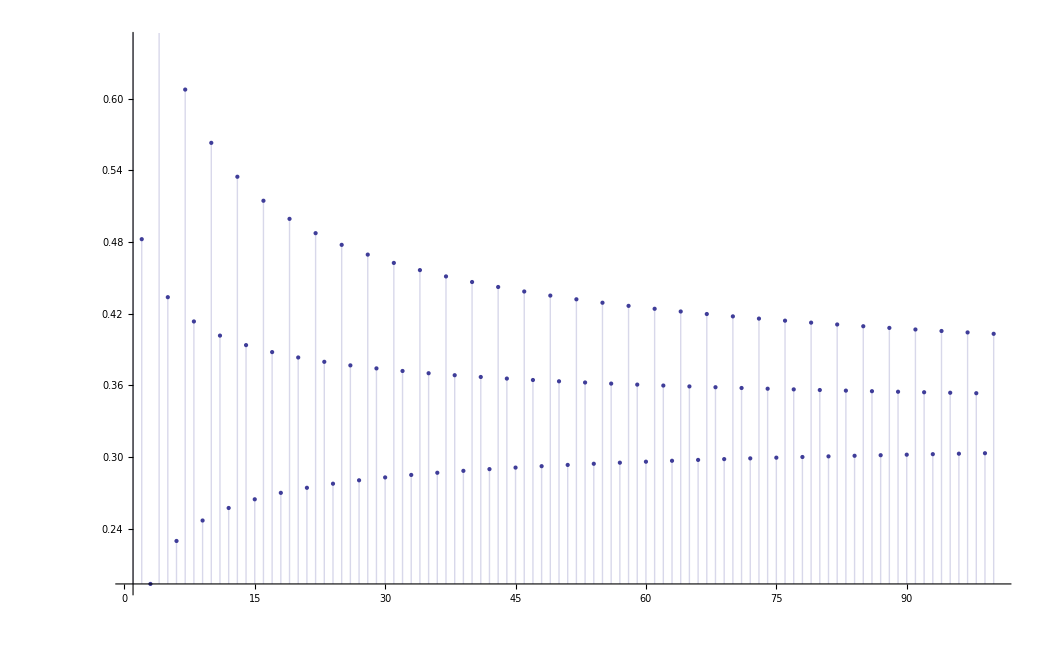

```mathematica
DiscretePlot[{ tx[n,.5,3/2]},{n,1,100,1}]
```

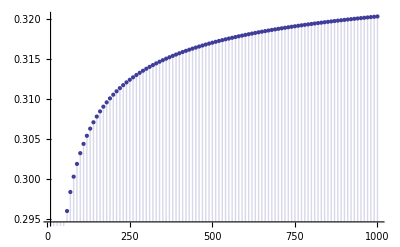

```mathematica
DiscretePlot[ tx2[n,.5,3/2],{n,10,1000,10}]
```

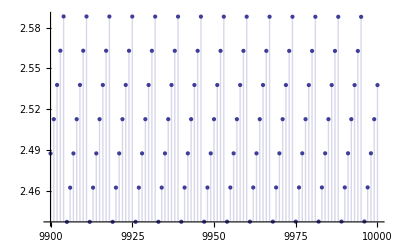

```mathematica
DiscretePlot[ {tx[n,.4,7]},{n,10000-100,10000}]
```

```mathematica
HarmonicNumber[n/4,s]/.n->100/.s->.5
```

8.63931

```mathematica
Zeta[.5]-Zeta[.5,1+100/4]
```

8.63931

```mathematica
D[Sum[ j^-s,{j,1,x n}],{x,3}]/.x->1
```

n^3 s (1+s) (2+s) (-HarmonicNumber[n,3+s]+Zeta[3+s])

```mathematica
D[Sum[ j^-s-(j+x n)^-s,{j,1,Infinity}],{x,3}]/.x->1
```

n^3 s (1+s) (2+s) HurwitzZeta[3+s,1+n]

```mathematica
D[(-x^(1-s))Sum[ j^-s, {j,1,n}],{x,3}]/.x->1
```

(-1-s) (1-s) s HarmonicNumber[n,s]

```mathematica
D[(1-x^(1-s))Zeta[s],{x,2}]/.x->1
```

(1-s) s Zeta[s]

```mathematica
FullSimplify[(D[Sum[ j^-s-(j+x n)^-s,{j,1,Infinity}]-x^(1-s)Sum[ j^-s, {j,1,n}],{x,3}]/.x->1)/((-1-s) (1-s) s)]
```

HarmonicNumber[n,s]+(n^3 (2+s) HurwitzZeta[3+s,1+n])/(-1+s)

```mathematica
ff[n_,s_]:=HarmonicNumber[n,s]+(n^3 (2+s) HurwitzZeta[3+s,1+n])/(-1+s)
```

```mathematica
ff[1000000000,N[ZetaZero[1]]]
```

-2.3703×10^-6-2.37262×10^-6 ⅈ

```mathematica
Zeta[.5]
```

-1.46035

```mathematica
FullSimplify[(D[Sum[ j^-s-(j+x n)^-s,{j,1,Infinity}]-x^(1-s)Sum[ j^-s, {j,1,n}],{x,2}]/.x->1)/((1-s) s)]
```

HarmonicNumber[n,s]+(n^2 (1+s) HurwitzZeta[2+s,1+n])/(-1+s)

```mathematica
al[n_,a_,b_]:=b (Floor[n/b]-Floor[(n-1)/b])-a (Floor[n/a]-Floor[(n-1)/a])
ala[n_,a_,b_]:=-a (Floor[n/a]-Floor[(n-1)/a])
alb[n_,a_,b_]:=b (Floor[n/b]-Floor[(n-1)/b])
```

```mathematica
N@Sum[(1/3) al[n,4,3]/(n/3)^2,{n,1,12*1000}]
```

0.411234

```mathematica
N@Limit[(1-x^(1-s))Zeta[s],s->2]/.x->(4/3)
```

0.411234

```mathematica
Table[ al[n,4,5],{n,1,20}]
```

{0,0,0,-4,5,0,0,-4,0,5,0,-4,0,0,5,-4,0,0,0,1}

```mathematica
Table[(n/5)^-2,{n,1,40}]
```

{25,25/4,25/9,25/16,1,25/36,25/49,25/64,25/81,1/4,25/121,25/144,25/169,25/196,1/9,25/256,25/289,25/324,25/361,1/16,25/441,25/484,25/529,25/576,1/25,25/676,25/729,25/784,25/841,1/36,25/961,25/1024,25/1089,25/1156,1/49,25/1296,25/1369,25/1444,25/1521,1/64}

```mathematica
Table[ala[n,5,6]n^-s,{n,1,60}]
```

{0,0,0,0,-5^(1-s),0,0,0,0,-2^-s 5^(1-s),0,0,0,0,-3^-s 5^(1-s),0,0,0,0,-4^-s 5^(1-s),0,0,0,0,-5^(1-2 s),0,0,0,0,-5^(1-s) 6^-s,0,0,0,0,-5^(1-s) 7^-s,0,0,0,0,-5^(1-s) 8^-s,0,0,0,0,-5^(1-s) 9^-s,0,0,0,0,-2^-s 5^(1-2 s),0,0,0,0,-5^(1-s) 11^-s,0,0,0,0,-5^(1-s) 12^-s}

```mathematica
Table[alb[n,5,6](n)^-s ,{n,1,30}]
```

{0,0,0,0,0,6^(1-s),0,0,0,0,0,2^(1-2 s) 3^(1-s),0,0,0,0,0,2^(1-s) 3^(1-2 s),0,0,0,0,0,2^(1-3 s) 3^(1-s),0,0,0,0,0,5^-s 6^(1-s)}

```mathematica
tt[n_,s_,a_,b_]:=Sum[ (a n+j)-s,{j,1,a}]-(a/b)^(1-s)Sum[ (b n+j)^-s,{j,1,b}]
```

```mathematica
tt[0,s,2,1]
```

3-2^(1-s)-2 s

```mathematica
N@Sum[(1/1) al[n,3,1](n/1)^-s,{n,1,2*2}]
```

1.+2.^(-1. s)-2. 3.^(-1. s)+4.^(-1. s)

```mathematica
ala[n_,a_,b_]:= -a(Floor[n/a]-Floor[(n-1)/a])
alb[n_,a_,b_]:= b(Floor[n/b]-Floor[(n-1)/b])
ala2[n_,a_,b_]:= (Floor[n/a]-Floor[(n-1)/a])
alb2[n_,a_,b_]:= (Floor[n/b]-Floor[(n-1)/b])
f1[nn_,s_,a_,b_]:=Sum[(1/b) al[n,a,b] (n/b)^-s,{n,1,(a b)nn}]
f2[nn_,s_,a_,b_]:=Sum[Sum[(1/b) al[a b n + j,a,b] ((n a b +j)/b)^-s,{j,1,a b}],{n,0,nn}]
f3[nn_,s_,a_,b_]:=(1/b)Sum[Sum[ al[j,a,b] ((n a b +j)/b)^-s,{j,1,a b}],{n,0,nn}]
f4[nn_,s_,a_,b_]:=b^(s-1)Sum[Sum[ al[j,a,b] ((n a b +j))^-s,{j,1,a b}],{n,0,nn}]
f5[nn_,s_,a_,b_]:=b^(s-1)Sum[Sum[ ala[j,a,b] ((n a b +j))^-s,{j,1,a b}]+Sum[ alb[j,a,b] ((n a b +j))^-s,{j,1,a b}],{n,0,nn}]
f6[nn_,s_,a_,b_]:=b^(s-1)Sum[Sum[ ala[j a,a,b] ((n a b +j a ))^-s,{j,1,b}]+Sum[ alb[j b,a,b] ((n a b +j b))^-s,{j,1,a}],{n,0,nn}]
f7[nn_,s_,a_,b_]:=b^(s-1)Sum[Sum[ -a ala2[j a,a,b] ((n a b +j a ))^-s,{j,1,b}]+Sum[ b alb2[j b,a,b] ((n a b +j b))^-s,{j,1,a}],{n,0,nn}]
f8[nn_,s_,a_,b_]:=b^(s-1)Sum[Sum[ -a  ((n a b +j a ))^-s,{j,1,b}]+Sum[ b  ((n a b +j b))^-s,{j,1,a}],{n,0,nn}]
f9[nn_,s_,a_,b_]:=b^(s-1)Sum[Sum[ -a  (a^-s)((n  b +j  ))^-s,{j,1,b}]+Sum[ b  (b^-s)((n a  +j ))^-s,{j,1,a}],{n,0,nn}]
f10[nn_,s_,a_,b_]:=b^(s-1)Sum[-a^(1-s)Sum[ ((n  b +j  ))^-s,{j,1,b}]+(b^(1-s))Sum[ ((n a  +j ))^-s,{j,1,a}],{n,0,nn}]
f11[nn_,s_,a_,b_]:=Sum[-a^(1-s)(1/b^(1-s))Sum[ ((n  b +j  ))^-s,{j,1,b}]+(b^(1-s))(1/b^(1-s))Sum[ ((n a  +j ))^-s,{j,1,a}],{n,0,nn}]
f12[nn_,s_,a_,b_]:=Sum[Sum[(n a+j)^-s,{j,1,a}]-(a/b)^(1-s)Sum[ (n  b +j )^-s,{j,1,b}],{n,0,nn}]
```

```mathematica
N@f12[1000,1,3,2]
```

0.405382

```mathematica
Sum[ j^-s-(j+a n)^-s,{j,1,Infinity}]-(a/b)^(1-s)Sum[ j^-s - (j+b n)^-s,{j,1,Infinity}]
```

-HurwitzZeta[s,1+a n]+Zeta[s]-(a/b)^(1-s) (-HurwitzZeta[s,1+b n]+Zeta[s])

```mathematica
D[-HurwitzZeta[s,1+a n]+Zeta[s]-(a/b)^(1-s) (-HurwitzZeta[s,1+b n]+Zeta[s]),b]/.b->1
```

-a^(1-s) n s HurwitzZeta[1+s,1+n]+a^(1-s) (1-s) (-HurwitzZeta[s,1+n]+Zeta[s])

```mathematica
d1[n_,s_,x_]:=Sum[j^-s - (j+n x)^-s,{j,1,Infinity}]-x^(1-s)Sum[ j^-s,{j,1,n}]
d2[n_,s_,x_]:=Sum[j^-s,{j,1,n}]-x^(1-s)Sum[ j^-s - (j+n/x)^-s,{j,1,Infinity}]
```

```mathematica
Table[FullSimplify[ (D[d1[n,s,x],{x,k}]/.x->1)/(D[(1-x^(1-s))Zeta[s],{x,k}]/.x->1)Zeta[s]],{k,1,5}]//TableForm
```

HarmonicNumber[n,s]+(n s HurwitzZeta[1+s,1+n])/(-1+s)
HarmonicNumber[n,s]+(n^2 (1+s) HurwitzZeta[2+s,1+n])/(-1+s)
HarmonicNumber[n,s]+(n^3 (2+s) HurwitzZeta[3+s,1+n])/(-1+s)
HarmonicNumber[n,s]+(n^4 (3+s) HurwitzZeta[4+s,1+n])/(-1+s)
HarmonicNumber[n,s]+(n^5 (4+s) HurwitzZeta[5+s,1+n])/(-1+s)

```mathematica
Table[FullSimplify[ (D[d2[n,s,x],{x,k}]/.x->1)/(D[(1-x^(1-s))Zeta[s],{x,k}]/.x->1)Zeta[s]],{k,1,5}]//TableForm
```

(-(-1+s) HurwitzZeta[s,1+n]+n s HurwitzZeta[1+s,1+n]+(-1+s) Zeta[s])/(-1+s)
(-(-1+s) HurwitzZeta[s,1+n]+2 n s HurwitzZeta[1+s,1+n]-n^2 (1+s) HurwitzZeta[2+s,1+n]+(-1+s) Zeta[s])/(-1+s)
(-(-1+s) HurwitzZeta[s,1+n]+3 n s HurwitzZeta[1+s,1+n]-3 n^2 (1+s) HurwitzZeta[2+s,1+n]+n^3 (2+s) HurwitzZeta[3+s,1+n]+(-1+s) Zeta[s])/(-1+s)
(-(-1+s) HurwitzZeta[s,1+n]+4 n s HurwitzZeta[1+s,1+n]-6 n^2 (1+s) HurwitzZeta[2+s,1+n]+4 n^3 (2+s) HurwitzZeta[3+s,1+n]-n^4 (3+s) HurwitzZeta[4+s,1+n]+(-1+s) Zeta[s])/(-1+s)
(-(-1+s) HurwitzZeta[s,1+n]+5 n s HurwitzZeta[1+s,1+n]-10 n^2 (1+s) HurwitzZeta[2+s,1+n]+10 n^3 (2+s) HurwitzZeta[3+s,1+n]-5 n^4 (3+s) HurwitzZeta[4+s,1+n]+n^5 (4+s) HurwitzZeta[5+s,1+n]+(-1+s) Zeta[s])/(-1+s)

```mathematica
dif[n_, s_, m_, k_] := n^m(s-1+m)(Zeta[s+m]-Sum[ 1/(j^(s+m)),{j,1,n}]) - n^k(s-1+k)(Zeta[s+k]-Sum[ 1/(j^(s+k)),{j,1,n}])
dif2[n_, s_, m_, k_] := {n^m(s-1+m)(Zeta[s+m]-Sum[ 1/(j^(s+m)),{j,1,n}]), n^k(s-1+k)(Zeta[s+k]-Sum[ 1/(j^(s+k)),{j,1,n}])}
```

```mathematica
FullSimplify[dif[n,s,m,k]]
```

-n^k (-1+k+s) HurwitzZeta[k+s,1+n]+n^m (-1+m+s) HurwitzZeta[m+s,1+n]

```mathematica
-n^k (-1+k+s) HurwitzZeta[k+s,1+n]+n^m (-1+m+s) HurwitzZeta[m+s,1+n]
```

-n^k (-1+k+s) HurwitzZeta[k+s,1+n]+n^m (-1+m+s) HurwitzZeta[m+s,1+n]

```mathematica
d3[n_,s_,m_,k_]:=-n^k (-1+k+s) HurwitzZeta[k+s,1+n]+n^m (-1+m+s) HurwitzZeta[m+s,1+n]
```

```mathematica
d3[100000000000.,0,.25+4I,.5+8I]
```

0.124969+1.9993 ⅈ

```mathematica
ark[n_,x_]:= Sum[ j^(-1/2+x) n^-x (1/2+x)- j^(-1/2-x)n^x (1/2-x),{j,1,n}]
ark2[n_,s_]:= (1-s)Sum[ j^-s,{j,1,n}]+s n^(1-2s)Sum[ j^(-1+s),{j,1,n}]
```

```mathematica
ark[1000000,14.134725141734695 ⅈ]
```

0.+0.0141347 ⅈ

```mathematica
N[ZetaZero[1]]
```

0.5+14.1347 ⅈ

```mathematica
ts[n_]:=n^(1-2(.1+ZetaZero[1]))
```

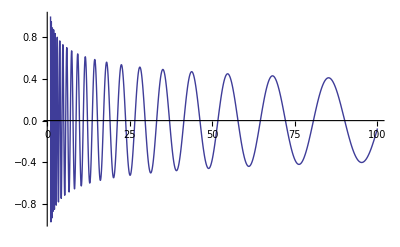

```mathematica
Plot[ Re[ts[n]],{n,1,100}]
```

```mathematica
ark2[12000,14.134725141734695 ⅈ]
```

70864.4-27477.3 ⅈ

```mathematica
ark3[n_,s_,x_]:= (1-s)(Zeta[s]-Sum[ 1/j^s,{j,1,n}])+(s-1+x) n^x (Zeta[s+x]-Sum[ 1/j^(s+x),{j,1,n}])
ark4[n_,s_,x_]:= (Sum[ 1/j^s,{j,1,n}])-(s-1+x) n^x /(1-s)(Zeta[s+x]-Sum[ 1/j^(s+x),{j,1,n}])
ark5[n_,s_,x_]:= {(Sum[ 1/j^s,{j,1,n}]),(s-1+x) n^x/(1-s) (Zeta[s+x]-Sum[ 1/j^(s+x),{j,1,n}])}
ark6[n_,s_,x_]:= {(1-s)(Zeta[s]-Sum[ 1/j^s,{j,1,n}]),(s-1+x) n^x (Zeta[s+x]-Sum[ 1/j^(s+x),{j,1,n}])}
```

```mathematica
ark4[10000000,.5+3I,1]
```

0.532685-0.0789056 ⅈ

```mathematica
Zeta[.5+3I]
```

0.532737-0.0788965 ⅈ

```mathematica
ark3[1000000000,.3+3I,.3]
```

-0.00023606-0.000183986 ⅈ

```mathematica
ark5[10000000,.5+3I,1]
```

{-1023.29-181.364 ⅈ,-1023.82-181.285 ⅈ}

```mathematica
ark6[10000000,.5+3I,1]
```

{1055.77-2980.83 ⅈ,-1055.77+2980.83 ⅈ}

```mathematica
ark3[n,s,1-2s]
```

-n^(1-2 s) s (-HarmonicNumber[n,1-s]+Zeta[1-s])+(1-s) (-HarmonicNumber[n,s]+Zeta[s])

```mathematica
ark7[n_,s_]:=n^(1-2 s) s HarmonicNumber[n,1-s]+(-1+s) HarmonicNumber[n,s]
ark7a[n_,s_]:={n^(1-2 s) s  HarmonicNumber[n,1-s],(-1+s) HarmonicNumber[n,s]}
```

```mathematica
ark7[100000000000,N[ZetaZero[1]]]
```

-5.84131×10^-6+0.0000443068 ⅈ

```mathematica
FullSimplify[-n^(1-2 s) s (-HarmonicNumber[n,1-s])+(1-s) (-HarmonicNumber[n,s])]
```

n^(1-2 s) s HarmonicNumber[n,1-s]+(-1+s) HarmonicNumber[n,s]

```mathematica
ark7a[100000000000,.6+I]
```

{24639.4-4884.31 ⅈ,-24638.7+4884.84 ⅈ}

```mathematica
ark9[n_,j_,x_]:=  j^(-1/2+x) n^-x (1/2+x)- j^(-1/2-x)n^x (1/2-x)
ark9t[n_,j_,x_,t_]:=  j^(-1/2+x) n^-(x t) (1/2+x)- j^(-1/2-x)n^(x t) (1/2-x)
ark9ts[n_,x_,t_]:=  Sum[ j^(-1/2+x) n^-(x t) (1/2+x)- j^(-1/2-x)n^(x t) (1/2-x),{j,1,n}]
ark10[n_,x_]:=(n^-x (1/2+x) HarmonicNumber[n,1/2-x])-(n^x (1/2-x) HarmonicNumber[n,1/2+x])
ark11[n_,x_]:=(  (1/2+x)HarmonicNumber[n,1/2-x])-(  (1/2-x)HarmonicNumber[n,1/2+x])
ark12[n_,x_]:=(n^-x  )-(n^x )
```

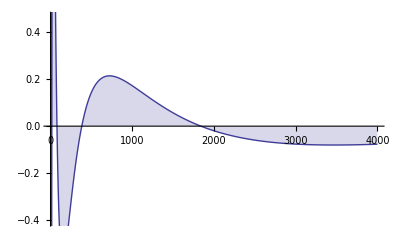

```mathematica
DiscretePlot[Re[ark9[100000000,j,.1+2I]],{j,1,4000}]
```

```mathematica
n^(1-2s)(n^(-1/2+s))
```

n^(1/2-s)

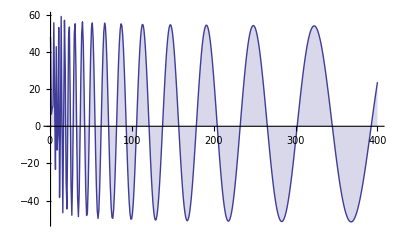

```mathematica
DiscretePlot[Im[ark9ts[j,3I+21.022039638771556 ⅈ,1]],{j,1,400,1}]
```

```mathematica
N[ZetaZero[2]]
```

0.5+21.022 ⅈ

```mathematica
Expand[ark9ts[n,x,1]]
```

1/2 n^-x HarmonicNumber[n,1/2-x]+n^-x x HarmonicNumber[n,1/2-x]-1/2 n^x HarmonicNumber[n,1/2+x]+n^x x HarmonicNumber[n,1/2+x]

```mathematica
FullSimplify@Sum[ j^(-1/2+x) n^-(x ) (1/2+x),{j,1,n}]
```

n^-x (1/2+x) HarmonicNumber[n,1/2-x]

```mathematica
FullSimplify@Sum[  j^(-1/2-x)n^(x) (1/2-x),{j,1,n}]
```

n^x (1/2-x) HarmonicNumber[n,1/2+x]

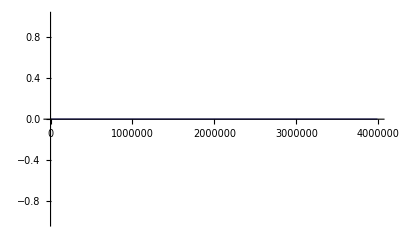

```mathematica
DiscretePlot[Re[ark10[j,122.94682929355258 ⅈ]],{j,1,4000000,10000}]
```

```mathematica
N[ZetaZero[40]]
```

0.5+122.947 ⅈ

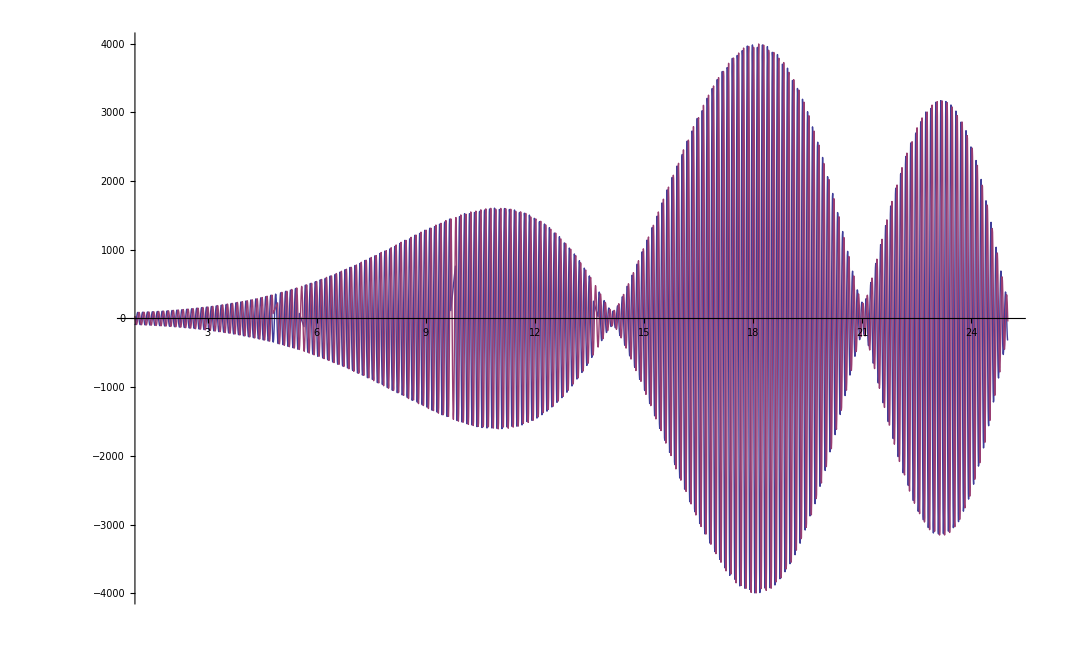

```mathematica
Plot[{Re[ark10[10^20,.1+s I]],Im[ark10[10^20,.1+s I]]},{s,1,25}]
```

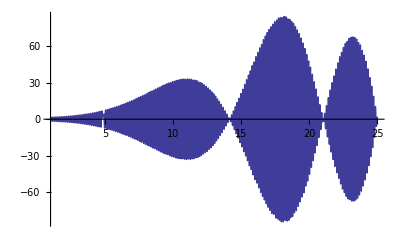

```mathematica
Plot[{Im[ark10[10^20,s I]]},{s,1,25}]
```

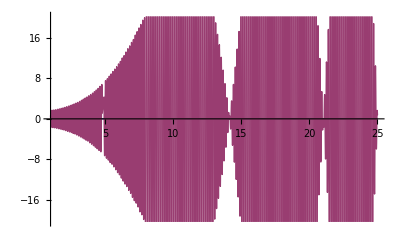

```mathematica
Plot[{Re[ark10z[10^20,s I]],Im[ark10z[10^20,s I]]},{s,1,25}]
```

```mathematica
N[ZetaZero[2]]
```

0.5+21.022 ⅈ

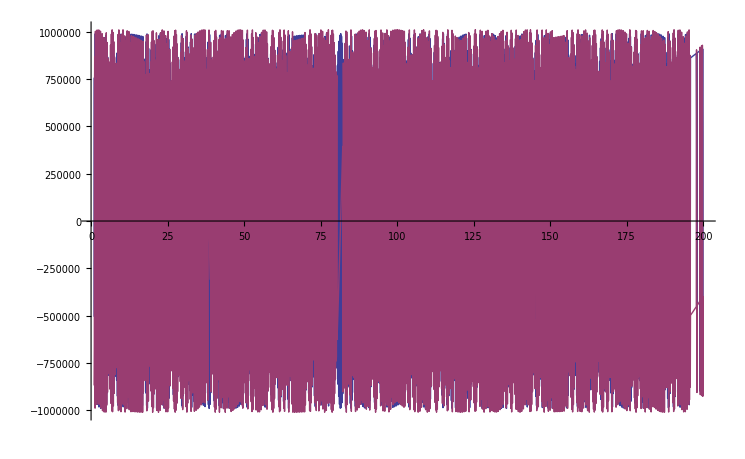

```mathematica
Plot[{Re[ark11[10^10,.1+s I]],Im[ark11[10^10,.1+s I]]},{s,1,200}]
```

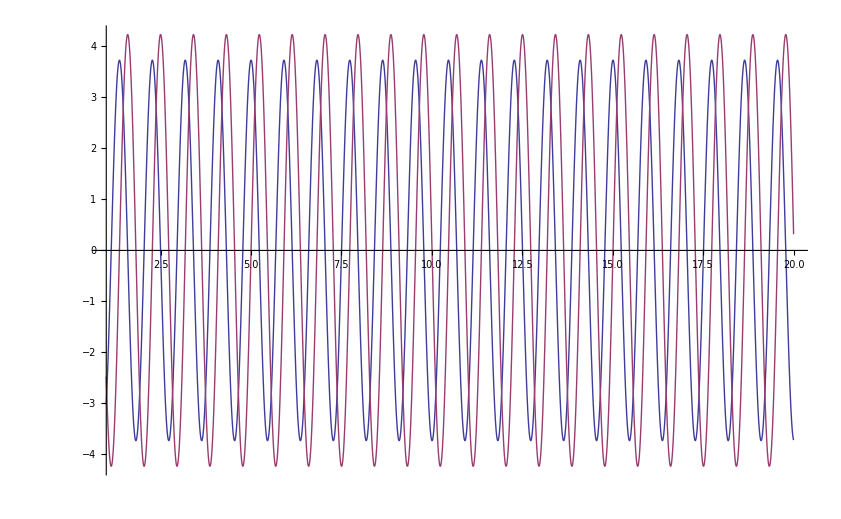

```mathematica
Plot[{Re[ark12[10^3,.2+s I]],Im[ark12[10^3,.2+s I]]},{s,1,20}]
```

```mathematica
ark10a[n_,x_]:=(n^-x (1/2+x) HarmonicNumber[n,1/2-x])-(n^x (1/2-x) HarmonicNumber[n,1/2+x])
ark11a[n_,x_]:=(  (1/2+x)HarmonicNumber[n,1/2-x])-(  (1/2-x)HarmonicNumber[n,1/2+x])
ark12a[n_,x_]:=(n^-x  )-(n^x )
```

```mathematica
FullSimplify[n^-x - n^x]
```

n^-x-n^x

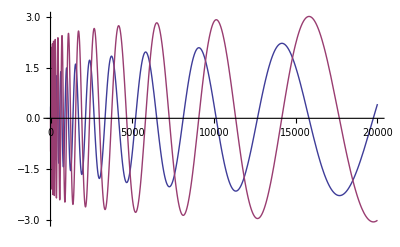

```mathematica
Plot[{Re[ark12[n,.1+14.134725141734695 ⅈ ]],Im[ark12[n,.1+14.134725141734695 ⅈ]]},{n,1,20000}]
```

```mathematica
N[ZetaZero[1]]
```

0.5+14.1347 ⅈ

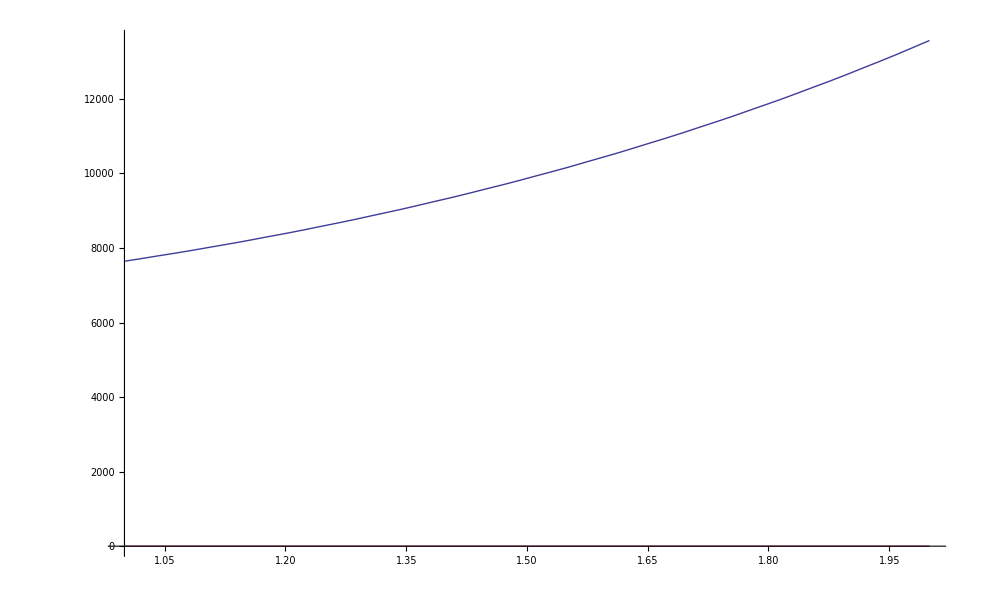

```mathematica
Plot[{(Re[ark10[10^20,.1+s I]])^2+(Im[ark10[10^20,.1+s I]]^2),-1},{s,1,2}]
```

```mathematica
ark10z[n_,x_]:=(n^-x (1/2+x)Zeta[1/2-x])-(n^x (1/2-x)Zeta[1/2+x])
ark10z2[n_,x_]:=(n^-x (1/2+x)(Zeta[1/2-x]-HarmonicNumber[n,1/2-x]))-(n^x (1/2-x)(Zeta[1/2+x]-HarmonicNumber[n,1/2+x]))
ark10z3[n_,x_]:=(n^-x (1/2+x)(n^(1-(1/2-x))/(1-(1/2-x))))-(n^x (1/2-x)(n^(1-(1/2+x))/(1-(1/2+x))))
ark10z4[n_,x_]:=(Zeta[1/2-x])-(Zeta[1/2+x])
ark10z5[n_,x_]:=( (1/2+x)Zeta[1/2-x])-( (1/2-x)Zeta[1/2+x])
ark10z6[n_,x_]:=(n^-x Zeta[1/2-x])-(n^x Zeta[1/2+x])
ark10z7[n_,x_]:=(n^-x  HarmonicNumber[n,1/2-x])-(n^x  HarmonicNumber[n,1/2+x])
```

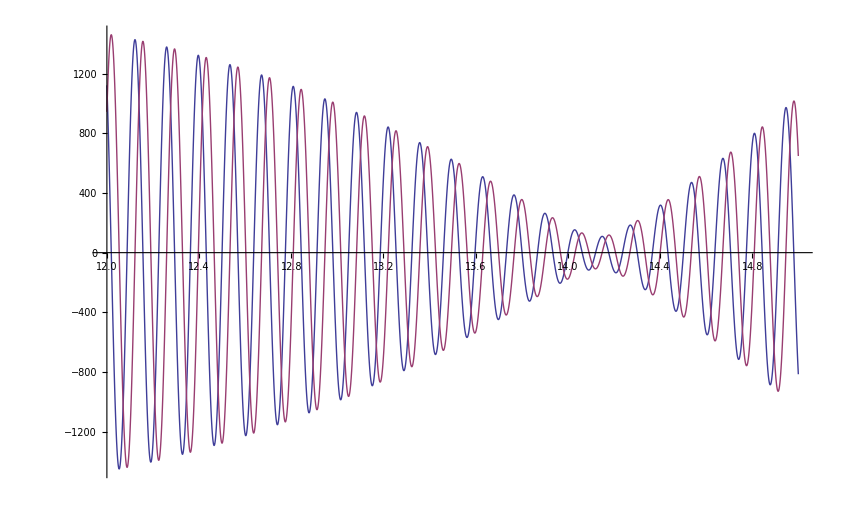

```mathematica
Plot[{Re[ark10z[10^20,.1+s I]],Im[ark10z[10^20,.1+s I]]},{s,12,15}]
```

```mathematica
(n^-x (1/2+x)(n^(1-(1/2-x))/(1-(1/2-x))))-(n^x (1/2-x)(n^(1-(1/2+x))/(1-(1/2+x))))
```

0

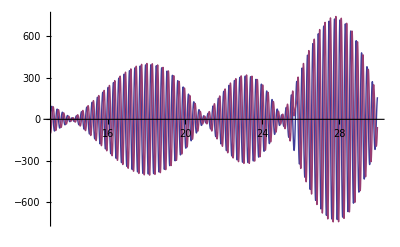

```mathematica
Plot[{Re[ark10z[10^10,.1+s I]],Im[ark10z[10^10,.1+s I]]},{s,13,30}]
```

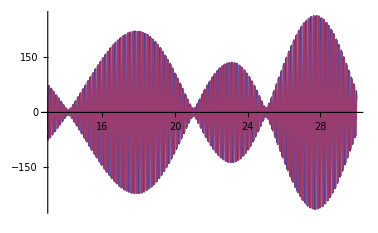

```mathematica
Plot[{Re[ark10z6[10^20,.1+s I]],Im[ark10z6[10^20,.1+s I]]},{s,13,30}]
```

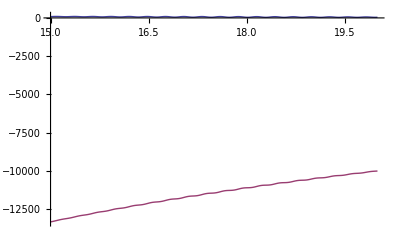

```mathematica
Plot[{Re[ark10z7[10^10,.1+s I]],Im[ark10z7[10^10,.1+s I]]},{s,15,20}]
```

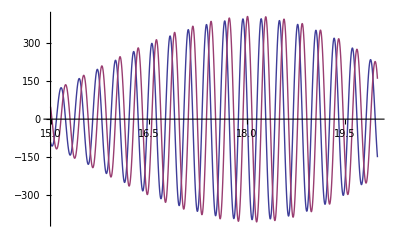

```mathematica
Plot[{Re[ark10[10^10,.1+s I]],Im[ark10[10^10,.1+s I]]},{s,15,20}]
```

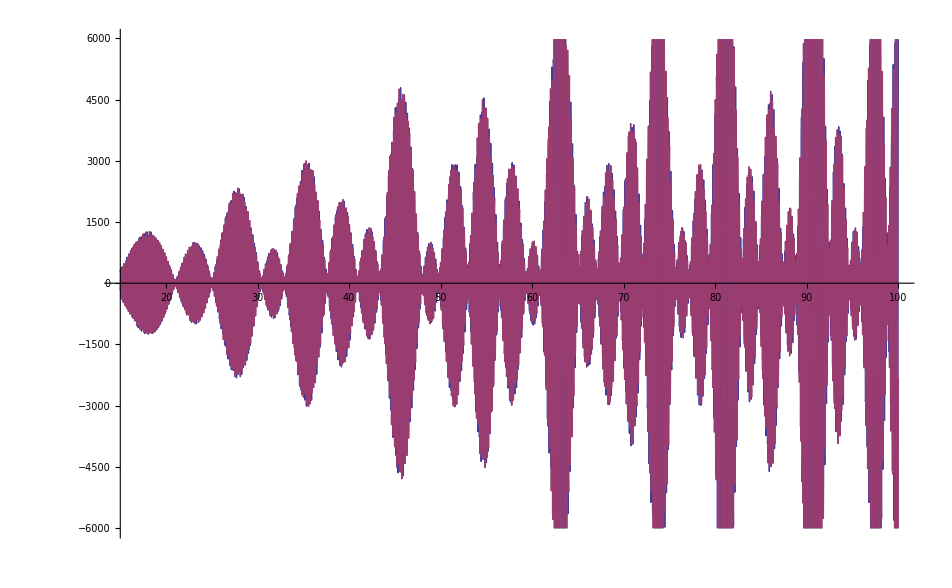

```mathematica
Plot[{Re[ark10[10^15,.1+s I]],Im[ark10[10^15,.1+s I]]},{s,15,100}]
```

```mathematica
pa[s_]:=Plot[ {Re[HarmonicNumber[n,s]-n^(1-s)/(1-s)],Im[HarmonicNumber[n,s]-n^(1-s)/(1-s)]},{n,1,10000000}]
pa2[s_]:=Plot[ {Re[HarmonicNumber[n,s]],Im[HarmonicNumber[n,s]]},{n,1,10000000}]
pa3[s_]:=Plot[ {Re[(Zeta[s]-HarmonicNumber[n,s])+n^(1-s)/(1-s)],Im[(Zeta[s]-HarmonicNumber[n,s])+n^(1-s)/(1-s)]},{n,1,10000000}]
```

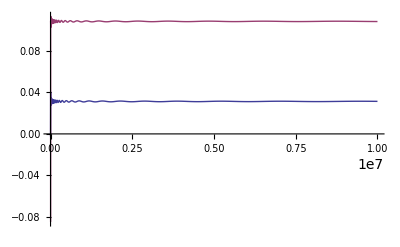

```mathematica
pa[N[ZetaZero[2]+.1I]]
```

```mathematica
ark10h1[n_,x_]:=(n^-x (1/2+x) HarmonicNumber[n,1/2-x])
ark10h2[n_,x_]:=(n^x (1/2-x) HarmonicNumber[n,1/2+x])
```

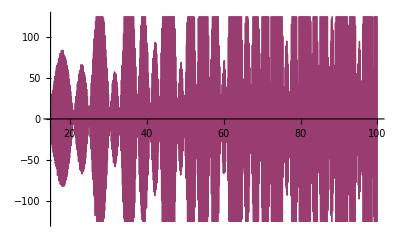

```mathematica
Plot[{Re[ark10h1[10^15,s I]-ark10h2[10^15,s I]],Im[ark10h1[10^15,s I]-ark10h2[10^15,s I]]},{s,15,100}]
```

```mathematica
ark20[n_,x_]:=(n^-x (1/2+x) HarmonicNumber[n,1/2-x])-(n^x (1/2-x) HarmonicNumber[n,1/2+x])
ark20a[n_,x_]:={ HarmonicNumber[n,1/2-x], HarmonicNumber[n,1/2+x]}
ark20s[n_,x_,s_]:=(n^-x (1/2+ x) HarmonicNumber[n,1/2- x])-(n^x (1/2- x) HarmonicNumber[n,1/2+x])
ark20z[n_,x_]:=(n^-x (1/2+x) Zeta[1/2-x])-(n^x (1/2-x)Zeta[1/2+x])
ark20za[n_,x_]:={ Zeta[1/2-x],Zeta[1/2+x]}
ark20f[n_,x_]:={{n^-x, (1/2+x) ,HarmonicNumber[n,1/2-x]},{n^x ,(1/2-x), HarmonicNumber[n,1/2+x]}}
```

```mathematica
N@ark20a[10^5,4I]
```

{64.3166+45.6794 ⅈ,64.3166-45.6794 ⅈ}

```mathematica
ark20za[10^20,4.0I]
```

{0.606784-0.0911121 ⅈ,0.606784+0.0911121 ⅈ}

```mathematica
N@ark20f[10^5,14.134725141734695 ⅈ]//Grid
```

0.807567+0.589776 ⅈ | 0.5+14.1347 ⅈ | -12.5386-18.5117 ⅈ
0.807567-0.589776 ⅈ | 0.5-14.1347 ⅈ | -12.5386+18.5117 ⅈ

```mathematica
FullSimplify[Expand[(a+b I)(1/2 + x I )(e +f I) ]-Expand[(a-b I)(1/2 -x I )(e -f I) ]]
```

ⅈ (a (f+2 e x)+b (e-2 f x))

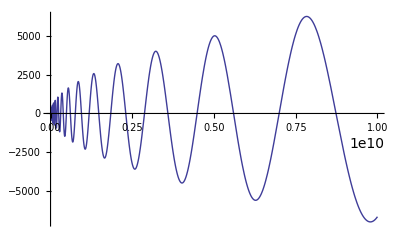

```mathematica
Plot[Re[HarmonicNumber[ n,1/2-z1]],{n,1,10000000000}]
```

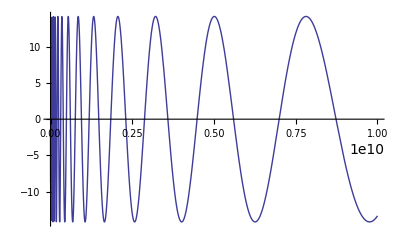

```mathematica
Plot[Re[(1/2+z1)n^-z1],{n,1,10000000000}]
```

```mathematica
Plot[Re[n^(1/2+z1)/(1/2+z1)],{n,1,10000000000}]
```

-Graphics-

```mathematica
z1 = (N@ZetaZero[1]-1/2)
```

0.+14.1347 ⅈ

```mathematica
(n^(1/2+z)/(1/2+z))((1/2+z)n^-z)
```

√n

```mathematica
ark40[n_,x_]:=(n^-x (1/2+x) HarmonicNumber[n,1/2-x])
ark41[n_,x_]:=(n^x (1/2-x) HarmonicNumber[n,1/2+x])
ark41b[n_,x_]:=(n^x  HarmonicNumber[n,1/2+x])
ark40a[n_,x_]:=(n^-x (1/2+x)( HarmonicNumber[n,1/2-x]-Zeta[1/2-x]))
ark42[n_,s_]:=Sum[ (n/j)^s / (j^(1/2)),{j,1,n}]
ark42a[n_,s_]:=Sum[ (n/j)^s ,{j,1,n}]
ark42b[n_,s_]:=Table[ (n/j)^s ,{j,1,n}]
ark45[n_,x_]:=(n^x  HarmonicNumber[n,x])
```

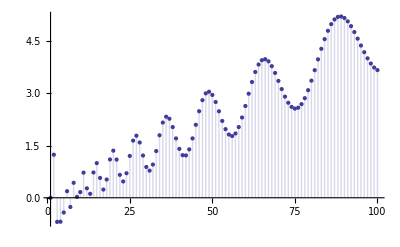

```mathematica
DiscretePlot[Im[ark45[n,.1I+N[ZetaZero[2]]]],{n,1,100}]
```

```mathematica
ark42b[30,s]
```

{30^s,15^s,10^s,(15/2)^s,6^s,5^s,(30/7)^s,(15/4)^s,(10/3)^s,3^s,(30/11)^s,(5/2)^s,(30/13)^s,(15/7)^s,2^s,(15/8)^s,(30/17)^s,(5/3)^s,(30/19)^s,(3/2)^s,(10/7)^s,(15/11)^s,(30/23)^s,(5/4)^s,(6/5)^s,(15/13)^s,(10/9)^s,(15/14)^s,(30/29)^s,1}

```mathematica
ark42b[31,s]
```

{31^s,(31/2)^s,(31/3)^s,(31/4)^s,(31/5)^s,(31/6)^s,(31/7)^s,(31/8)^s,(31/9)^s,(31/10)^s,(31/11)^s,(31/12)^s,(31/13)^s,(31/14)^s,(31/15)^s,(31/16)^s,(31/17)^s,(31/18)^s,(31/19)^s,(31/20)^s,(31/21)^s,(31/22)^s,(31/23)^s,(31/24)^s,(31/25)^s,(31/26)^s,(31/27)^s,(31/28)^s,(31/29)^s,(31/30)^s,1}

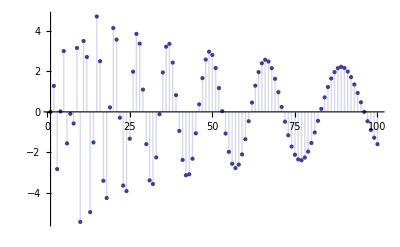

```mathematica
DiscretePlot[Im[n^(N[ZetaZero[2]])-(n-1)^(N[ZetaZero[2]])],{n,1,100}]
```

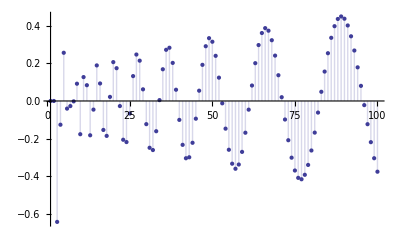

```mathematica
DiscretePlot[  Im[  HarmonicNumber[n-1,N[ZetaZero[2]]  ]  ],{n,1,100}]
```

```mathematica
teo[z_]:=DiscretePlot[  Im[ ( n^z)(HarmonicNumber[n,z])  ],{n,1,100}]
te[z_]:=DiscretePlot[  Im[ ( n^z-(n-1)^z)(HarmonicNumber[n-1,z])  ],{n,1,100}]
te2[z_]:=DiscretePlot[  Re[ ( n^(-1+z)z )(HarmonicNumber[n-1,z])  ],{n,1,100}]
te3[s_]:=DiscretePlot[Re[Sum[ (n/j)^s ,{j,1,n}]],{n,1,100}]
te3x[m_]:=Animate[DiscretePlot[Re[ m  Sum[ (n/j)^(.5+t I) ,{j,m,n,m}]],{n,1,100}, PlotRange->8],{t,14,15}]
te3y[m_]:=Animate[DiscretePlot[Re[  n/(-.5+t I)],{n,1,100}, PlotRange->8],{t,14,15}]
```

```mathematica
te3x[1/2]
```

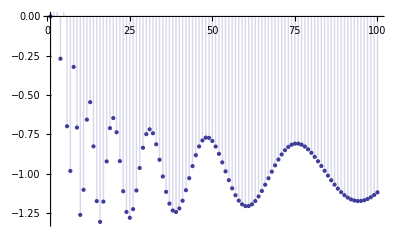

```mathematica
te2[N[ZetaZero[1]+.1]]
```

```mathematica
D[n^z,n]
```

n^(-1+z) z

```mathematica
Clear[da]
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
da[n_,s_,k_]:=da[n,s,k]=Sum[ j^-s da[Floor[n/j],s,k-1],{j,2,n}]
da[n_,s_,0]:=UnitStep[n-1]
dz[n_,s_,z_]:=Sum[ bin[z,k]da[n,s,k],{k,0,Log2@n}]
te4[z_,x_]:=DiscretePlot[  Re[ n^(x z)(dz[n,z,x])  ],{n,1,300}]
te5[z_,x_]:=DiscretePlot[  Re[ (dz[n,z,x])  ],{n,1,300}]
te6[s_]:=DiscretePlot[ Im[D[ n^(z s)(dz[n,s,z]),z]/.z->0  ],{n,1,500}]
```

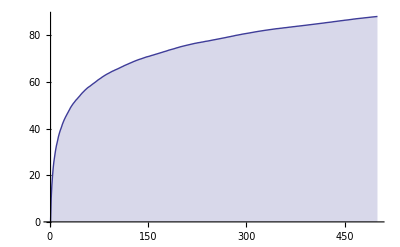

```mathematica
te6[N[ZetaZero[1]]]
```

```mathematica
D[ 100^(z s)(dz[100,s,z]),z]/.z->0/.s->1
```

292149953504274361788974787095433526022627/139440750459424954329067617870624607113600+Log[100]

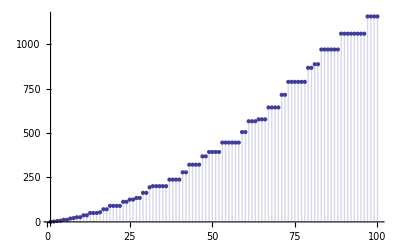

```mathematica
DiscretePlot[ D[ dz[n,-1,z],z]/.z->0,{n,1,100}]
```

```mathematica
D[ (dz[100,s,z]),z]/.z->0/.s->1
```

292149953504274361788974787095433526022627/139440750459424954329067617870624607113600

```mathematica
N[ZetaZero[1]]
```

0.5+14.1347 ⅈ

```mathematica
Limit[m  Sum[ (n/j)^z ,{j,m,n,m}],m->0]
```

Limit[m Sum[(n/j)^z,{j,m,n,m}],m→0]

```mathematica
Integrate[ (n/j)^z,{j,0,n}]
```

ConditionalExpression[-n/(-1+z),Re[z]<1&&n>0]